```mathematica
2-2
```

0

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

# Quantum Motion of a Particle in a Box

Nicholas Wheeler
Reed College Physics Department
20 August 2008

### Introduction

In Part 2 we studied solutions of

-ℏ^2/(2m)(∂_(x,x) +∂_(y,y))ψ[x,y,t]=ⅈ ℏ ∂_t ψ[x,y,t]

which vanish on the boundaries of the unit box: 0 < {x, y} < 1. We were, in particular, led to the normalized eigenfunctions

```mathematica
Ψ[x_,y_,m_,n_]:=2 Sin[m π x]Sin[n π y]
```

```mathematica
{{Plot3D[Ψ[x,y,1,1], {x,0,1},{y,0,1}, Ticks->False],
Plot3D[Ψ[x,y,1,2], {x,0,1},{y,0,1}, Ticks->False],Plot3D[Ψ[x,y,1,3], {x,0,1},{y,0,1}, Ticks->False]},
{Plot3D[Ψ[x,y,2,1], {x,0,1},{y,0,1}, Ticks->False],
Plot3D[Ψ[x,y,2,2], {x,0,1},{y,0,1}, Ticks->False],
Plot3D[Ψ[x,y,2,3], {x,0,1},{y,0,1}, Ticks->False]},
{Plot3D[Ψ[x,y,3,1], {x,0,1},{y,0,1}, Ticks->False],
Plot3D[Ψ[x,y,3,2], {x,0,1},{y,0,1}, Ticks->False],
Plot3D[Ψ[x,y,3,3], {x,0,1},{y,0,1}, Ticks->False]}}//MatrixForm
```

(-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-)

These we assembled into normalized functions

Ψ[x,y]=∑_m ∑_n C_mn Ψ[x,y,m,n]

∑_m ∑_n  C_mn(C̄)_mn=1

which we launched into motion by introduction of appropriate exponential "buzz factors"

Ψ[x,y,t]=∑_m ∑_n C_mn Ψ[x,y,m,n]ⅇ^(-ⅈ ω[m,n]t)

ω[m,n]=π^2(m^2+n^2)

We looked first to cases of the form

Ψ[x,y]=a[x]b[y]=∑_m ∑_n A_m B_n Ψ[x,y,m,n]

∑_m  A_m(Ā)_m=∑_n  B_n(B̄)_n 1

which give rise to probability densities of the factored form

P[x,y,t]=f[x,t]*g[y,t]

In such cases x and y are at all times statistically independent. We identified cases in which the expected position

{⟨x⟩_t,⟨y⟩_t}=∫_0^1 ∫_0^1 {x,y}P[x,y,t]ⅆxⅆy

traces a Lissajous figure. And other cases in which P[x, y, t] itself has the form (at least briefly) of a localized pimple tracing a Lissagous curve.

Then, following Chen et al, we looked to cases in which  P[x, y, 0] does not factor (x and y are no longer statistically independent), but which derive interest from the fact that P[x, y, 0] assumes significant value only on a specified Lissajous curve.  It is about some properties of cases of the latter sort that I propose now to speak.

### Simplest non-factorable boxed wavefunctions

The simplest way to linearly combine the moving normalized eigenfunctions

```mathematica
Ψ[x_,y_,m_,n_,t_]:=Ψ[x,y,m,n]*ⅇ^(-ⅈ ω[m,n] t)
ω[m_,n_]:=π^2(m^2+n^2)
```

is pairwise, the general (already normalized) form being

```mathematica
Ψ[x_,y_,m_,n_,p_,q_,α_,β_,t_]:=Cos[α]Ψ[x,y,m,n,t]+ⅇ^(ⅈ β)Sin[α]Ψ[x,y,p,q,t]
```

where α is a "mixing angle" and β is a "relative phase angle."

```mathematica
Ψ[x,y,m,n,p,q,α,β,t]
```

2 ⅇ^(-ⅈ (m^2+n^2) π^2 t) Cos[α] Sin[m π x] Sin[n π y]+2 ⅇ^(-ⅈ π^2 (p^2+q^2) t+ⅈ β) Sin[p π x] Sin[π q y] Sin[α]

```mathematica
Ψstar[x_,y_,m_,n_,p_,q_,α_,β_,t_]:=CompConj[Ψ[x,y,m,n,p,q,α,β,t]]
```

```mathematica
Ψstar[x,y,m,n,p,q,α,β,t]
```

2 ⅇ^(ⅈ (m^2+n^2) π^2 t) Cos[α] Sin[m π x] Sin[n π y]+2 ⅇ^(ⅈ π^2 (p^2+q^2) t-ⅈ β) Sin[p π x] Sin[π q y] Sin[α]

```mathematica
P[x_,y_,m_,n_,p_,q_,α_,β_,t_]:=Ψstar[x,y,m,n,p,q,α,β,t]*Ψ[x,y,m,n,p,q,α,β,t]
```

Proceeding

```mathematica
P[x,y,m,n,p,q,α,β,t]//Expand
```

4 Cos[α]^2 Sin[m π x]^2 Sin[n π y]^2+4 ⅇ^(-ⅈ (m^2+n^2) π^2 t+ⅈ π^2 (p^2+q^2) t-ⅈ β) Cos[α] Sin[m π x] Sin[p π x] Sin[n π y] Sin[π q y] Sin[α]+4 ⅇ^(ⅈ (m^2+n^2) π^2 t-ⅈ π^2 (p^2+q^2) t+ⅈ β) Cos[α] Sin[m π x] Sin[p π x] Sin[n π y] Sin[π q y] Sin[α]+4 Sin[p π x]^2 Sin[π q y]^2 Sin[α]^2

```mathematica
ExpToTrig[4 ⅇ^(-ⅈ (m^2+n^2) π^2 t+ⅈ π^2 (p^2+q^2) t-ⅈ β)+4 ⅇ^(ⅈ (m^2+n^2) π^2 t-ⅈ π^2 (p^2+q^2) t+ⅈ β)]
```

8 Cos[(m^2+n^2) π^2 t-π^2 (p^2+q^2) t+β]

we see that P[x, y, m, n, p, q, α, β, t] moves (oscillates) except when

m^2+n^2=p^2+q^2

The following source

```mathematica
Hyperlink["Integers as sums of two squares","http://www.math.mtu.edu/mathlab/COURSES/holt/dnt/represent3.html"]
```

indicates that

1^2+7^2=5^2+5^5=50

provides the smallest nontrivial instance of such a coincidence. But we will—in what immediately follows—have as much or more to do with "trivial" instances (of the form a^2+b^2=b^2+a^5=N) than with non-trivial ones.

Illustrative case 1:

```mathematica
Ψ[x,y,2,1,1,2,α,β,t]/.{α->ArcCos[2/3],β->ArcTan[2]}
```

```mathematica
4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+2/3  ⅇ^(-5 ⅈ π^2 t+ⅈ ArcTan[2]) Sin[π x] Sin[2 π y]
```

```mathematica
ⅇ^(ⅈ ArcTan[2])//ComplexExpand
```

(1+2 ⅈ)/(√5)

```mathematica
Ψ1= ⅇ^(-5 ⅈ π^2 t)( 4/3 Sin[2 π x] Sin[π y]+2/3 √5(1+2 ⅈ)/(√5)  Sin[π x] Sin[2 π y])
```

ⅇ^(-5 ⅈ π^2 t) (4/3 Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) Sin[π x] Sin[2 π y])

It is because (trivially)

2^2+1^1=1^2+2^2=5

that only a single time factor enters (multiplicatively) into the description of Ψ1, with the consequence that the associated probability density is time-independent:

```mathematica
Ψ1star= ⅇ^(+5 ⅈ π^2 t)( 4/3 Sin[2 π x] Sin[π y]+2/3 √5(1-2 ⅈ)/(√5)  Sin[π x] Sin[2 π y])
```

ⅇ^(5 ⅈ π^2 t) (4/3 Sin[2 π x] Sin[π y]+(2/3-(4 ⅈ)/3) Sin[π x] Sin[2 π y])

```mathematica
Ψ1star*Ψ1//FullSimplify
```

16/9 (4 Cos[π x]^2+4 Cos[π x] Cos[π y]+5 Cos[π y]^2) Sin[π x]^2 Sin[π y]^2

```mathematica
P1[x_,y_]:=16/9 (4 Cos[π x]^2+4 Cos[π x] Cos[π y]+5 Cos[π y]^2) Sin[π x]^2 Sin[π y]^2
```

```mathematica
Plot3D[P1[x,y],{x,0,1},{y,0,1}, Ticks->False]
```

-Graphics3D-

Illustrative Case 2:

This is but a slight variant of the preceding case, and again leads to a static probability density.

```mathematica
Ψ[x,y,3,1,1,3,α,β,t]/.{α->π/4,β->π/2}
```

√2 ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+√2 ⅇ^((ⅈ π)/2-10 ⅈ π^2 t) Sin[π x] Sin[3 π y]

```mathematica
ⅇ^((ⅈ π)/2)//ComplexExpand
```

ⅈ

```mathematica
Ψ2=√2 ⅇ^(-10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]+ ⅈ Sin[π x] Sin[3 π y])
```

√2 ⅇ^(-10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]+ⅈ Sin[π x] Sin[3 π y])

Only a single time factor remains, this time for the trivial reason

```mathematica
3^2+1^2=1^2+3^2=10
```

and as before, the probability density is static:

```mathematica
Ψ2star=√2 ⅇ^(+10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]- ⅈ Sin[π x] Sin[3 π y])
```

√2 ⅇ^(10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]-ⅈ Sin[π x] Sin[3 π y])

```mathematica
Ψ2star*Ψ2//FullSimplify
```

2 (Sin[3 π x]^2 Sin[π y]^2+Sin[π x]^2 Sin[3 π y]^2)

```mathematica
P2[x_,y_]:=2 (Sin[3 π x]^2 Sin[π y]^2+Sin[π x]^2 Sin[3 π y]^2)
```

```mathematica
Plot3D[P2[x,y],{x,0,1},{y,0,1}, Ticks->False]
```

-Graphics3D-

Illustrative Case 3:

```mathematica
Ψ[x,y,3,1,1,2,α,β,t]/.{α->π/4,β->π/2}
```

√2 ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+√2 ⅇ^((ⅈ π)/2-5 ⅈ π^2 t) Sin[π x] Sin[2 π y]

In this case

3^2+1^2=10
1^1+2^2=5

are distinct and so we can expect the probability density to move (oscillate).

```mathematica
Ψ3=√2 (ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ ⅈ ⅇ^(-5 ⅈ π^2 t)Sin[π x] Sin[2 π y])
```

√2 (ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ⅈ ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])

```mathematica
Ψ3star=√2 (ⅇ^(+10 ⅈ π^2 t) Sin[3 π x] Sin[π y]- ⅈ ⅇ^(+5 ⅈ π^2 t)Sin[π x] Sin[2 π y])
```

√2 (ⅇ^(10 ⅈ π^2 t) Sin[3 π x] Sin[π y]-ⅈ ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])

```mathematica
Ψ3star*Ψ3//FullSimplify
```

2 (-4 (1+2 Cos[2 π x]) Cos[π y] Sin[5 π^2 t] Sin[π x]^2 Sin[π y]^2+Sin[3 π x]^2 Sin[π y]^2+Sin[π x]^2 Sin[2 π y]^2)

```mathematica
P3[x_,y_,t_]:=2 (-4 (1+2 Cos[2 π x]) Cos[π y] Sin[5 π^2 t] Sin[π x]^2 Sin[π y]^2+Sin[3 π x]^2 Sin[π y]^2+Sin[π x]^2 Sin[2 π y]^2)
```

This function is seen to oscillate with angular frequency 5 π^2, as shown below:

```mathematica
Manipulate[Plot3D[P3[x,y,(2π)/(50 π^2)k],{x,0,1},{y,0,1}, Ticks->False, PlotRange->{0,6}], {k,0,10,1}]
```

The preceding examples (which I have borrowed from Mahoney, Paganin & Faulkner) will now be used  to expose the main points of this essay.

### From probability current to quantum vorticity

Let us, for the purposes of the present argument, reinstate the physical parameters m and ℏ. Let  Ψ[x, y, t] be written in polar form

```mathematica
Ψ=R Exp[ⅈ/ℏ S];
Ψstar=R Exp[-ⅈ/ℏ S];
```

with

```mathematica
R=r[x,y,t];
S=s[x,y,t];
```

Supposing Ψ[x, y, t] to be a solution of the free-particle Schrödinger equation, we construct

```mathematica
Schrödinger=Exp[-ⅈ/ℏ S](-ℏ^2/(2m)(D[Ψ,{x,2}]+D[Ψ,{y,2}])-ⅈ ℏ D[Ψ,t])//Expand
```

-ⅈ ℏ r^(0,0,1)[x,y,t]+r[x,y,t] s^(0,0,1)[x,y,t]-(ⅈ ℏ r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] (s^(0,1,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(0,2,0)[x,y,t])/(2 m)-(ⅈ ℏ r[x,y,t] s^(0,2,0)[x,y,t])/(2 m)-(ⅈ ℏ r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] (s^(1,0,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(2,0,0)[x,y,t])/(2 m)-(ⅈ ℏ r[x,y,t] s^(2,0,0)[x,y,t])/(2 m)

from which we extract and massage the real and imaginary parts (which must vanish separately):

```mathematica
(CompConj[Schrödinger]+Schrödinger)/(2  r[x,y,t])//Expand
(CompConj[Schrödinger]-Schrödinger)/(2 ℏ ⅈ)//Expand
```

s^(0,0,1)[x,y,t]+((s^(0,1,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(0,2,0)[x,y,t])/(2 m r[x,y,t])+((s^(1,0,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(2,0,0)[x,y,t])/(2 m r[x,y,t])

r^(0,0,1)[x,y,t]+(r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/(2 m)+(r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/(2 m)

The first equation can be written

s^(0,0,1)[x,y,t]+((s^(0,1,0)[x,y,t])^2)/(2 m)+((s^(1,0,0)[x,y,t])^2)/(2 m)=(ℏ^2( r^(2,0,0)[x,y,t]+r^(0,2,0)[x,y,t]))/(2 m r[x,y,t])

where in classical theory (ℏ ↓ 0) the expression on the left would vanish by appeal to Hamilton-Jacobi theory. The second equation finds employment at the end of the next paragraph.

The probability density is given now by

```mathematica
Ψstar *Ψ
```

r[x,y,t]^2

and the probability current by

```mathematica
Subscript[J, x]=ℏ/(2m ⅈ)(Ψstar D[Ψ,x]-Ψ D[Ψstar,x])//Simplify
Subscript[J, y]=ℏ/(2m ⅈ)(Ψstar D[Ψ,y]-Ψ D[Ψstar,y])//Simplify
```

(r[x,y,t]^2 s^(1,0,0)[x,y,t])/m

(r[x,y,t]^2 s^(0,1,0)[x,y,t])/m

which can be expressed

probability current=(probability density)*Grad[s]/m

The continuity equation that provides a local account of probability conservation lends interest to a construction

```mathematica
D[r[x,y,t]^2,t]+D[(r[x,y,t]^2 Derivative[1,0,0][s][x,y,t])/m,x]+D[(r[x,y,t]^2 Derivative[0,1,0][s][x,y,t])/m,y]//Expand
```

2 r[x,y,t] r^(0,0,1)[x,y,t]+(2 r[x,y,t] r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t]^2 s^(0,2,0)[x,y,t])/m+(2 r[x,y,t] r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t]^2 s^(2,0,0)[x,y,t])/m

that after only a little massaging leads to a construction that has already been shown to vanish:

```mathematica
%/r[x,y,t]//Expand
```

2 r^(0,0,1)[x,y,t]+(2 r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/m+(2 r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/m

```mathematica
%==(CompConj[Schrödinger]-Schrödinger)/(ℏ ⅈ)//Expand
```

True

The vector-valued construction

(probability current)/(probability density)

has the physical dimension of a "velocity." It becomes natural in this light to write

quantum mechanical velocity field ≡ (probability current)/(probability density)=1/m Grad[S]

The velocity field

(V_x[x,y,t]
V_y[x,y,t])=(J_x[x,y,t]
J_y[x,y,t])/P[x,y,t]=1/m Grad[S]

exists except where the probability density P[x,y,z,t] vanishes (which is to say: where Ψ[x,y,z,t] vanishes), and might exist even at such points if  J[x,y,z,t] happened also to vanish in just the right way. At those points the phase must be undifferentiable (discontinuous).

In fluid dynamics (see, for example, §1.2—"Rotation and Vorticity"—pages 19-31 in A. J. Chorin & J. E. Marsden, A Mathematical Introduction to Fluid Mechanics (2nd edition, 1990)) the vector-valued field produced by constructing the curl of a velocity field is called the "vorticity," denoated Ω:

Ω=Curl[V]

For the "quantum mechanical probability fluid" the vorticity vanishes

Ω=1/m Curl[ Grad[S]]=0

except at singular points (points where phase discontinuities cause  Grad[S]  to be undefined).

### Concrete implications of the general theory

REMARK: We are working in two dimensions, so trhe probability current and Grad[s] are 2-vectors, while the vorticity Ω is effectively a scalar (z-component of a 3-vector).

```mathematica
Needs["VectorFieldPlots`"]
```

Application to Illustrative Case 1

This was the static case illustrated below:

-Graphics3D-

The probability density vanishes at the center of the box

```mathematica
P1[1/2,1/2]
```

0

where (therefore) the vorticity becomes singular. 

We construct and plot the probability current, which is seen to circulate (steadily) around the singularity:

```mathematica
-ⅈ(Ψ1star D[Ψ1,x]-Ψ1 D[Ψ1star,x])//ComplexExpand
-ⅈ(Ψ1star D[Ψ1,y]-Ψ1 D[Ψ1star,y])//ComplexExpand
```

-64/9 π Cos[2 π x] Sin[π x] Sin[π y] Sin[2 π y]+32/9 π Cos[π x] Sin[2 π x] Sin[π y] Sin[2 π y]

64/9 π Cos[2 π y] Sin[π x] Sin[2 π x] Sin[π y]-32/9 π Cos[π y] Sin[π x] Sin[2 π x] Sin[2 π y]

```mathematica
J1X[x_,y_]:=-64/9 π Cos[2 π x] Sin[π x] Sin[π y] Sin[2 π y]+32/9 π Cos[π x] Sin[2 π x] Sin[π y] Sin[2 π y]
J1Y[x_,y_]:=64/9 π Cos[2 π y] Sin[π x] Sin[2 π x] Sin[π y]-32/9 π Cos[π y] Sin[π x] Sin[2 π x] Sin[2 π y]
```

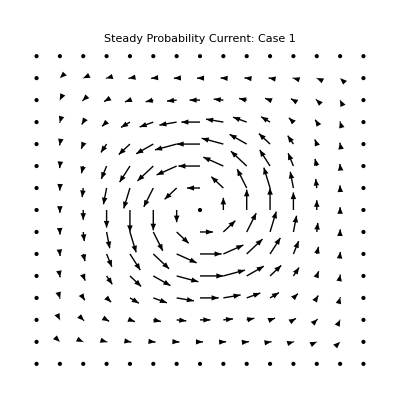

```mathematica
VectorFieldPlot[{J1X[x,y],J1Y[x,y]},{x,0,1},{y,0,1},PlotLabel->"Steady Probability Current: Case 1", LabelStyle->Directive[Bold, Red]]
```

We construct and plot the associated velocity field (after modification of the denominator to keep Mathematica from complaining)

```mathematica
V1X[x_,y_]:=J1X[x,y]/(P1[x,y]+0.000001)
V1Y[x_,y_]:=J1Y[x,y]/(P1[x,y]+0.000001)
```

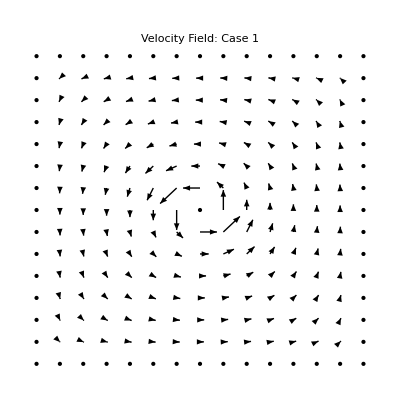

```mathematica
VectorFieldPlot[{V1X[x,y],V1Y[x,y]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field: Case 1", LabelStyle->Directive[Bold, Red]]
```

which places us in position to construct and plot the vorticity:

```mathematica
D[V1Y[x, y], x] - D[V1X[x, y], y]//Simplify//Chop
```

(-0.000280735 Cos[π y]^2 Sin[π x]^3 Sin[π y]-0.000280735 Cos[π x]^2 Sin[π x] Sin[π y]^3+0.000280735 Sin[π x]^3 Sin[π y]^3)/(1.×10^-6+7.11111 Cos[π x]^2 Sin[π x]^2 Sin[π y]^2+7.11111 Cos[π x] Cos[π y] Sin[π x]^2 Sin[π y]^2+8.88889 Cos[π y]^2 Sin[π x]^2 Sin[π y]^2)^2

```mathematica
Ω1[x_,y_]:=(-0.00028073541407543063 Cos[π y]^2 Sin[π x]^3 Sin[π y]-0.00028073541407543063 Cos[π x]^2 Sin[π x] Sin[π y]^3+0.00028073541407543063 Sin[π x]^3 Sin[π y]^3)/(1.*^-6+7.111111111111111 Cos[π x]^2 Sin[π x]^2 Sin[π y]^2+7.111111111111111 Cos[π x] Cos[π y] Sin[π x]^2 Sin[π y]^2+8.88888888888889 Cos[π y]^2 Sin[π x]^2 Sin[π y]^2)^2
```

```mathematica
Plot3D[Ω1[x,y],{x,0,1},{y,0,1}, PlotRange->{0,10},PlotPoints->{100}, Ticks->False,PlotLabel->"Vorticity: Case 1", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

The figure indicates that the vorticity vanishes everywhere except at the singularity, where it acquires the character of a delta function.

Though the amplitude of the wavefunction is (in the present example) time-independent

```mathematica
Ψ1
```

ⅇ^(-5 ⅈ π^2 t) (4/3 Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) Sin[π x] Sin[2 π y])

(as are all things derived from it: probability density, probability current, vorticity), its phase is time-dependent—with

```mathematica
Period=2/(5π)
```

2/(5 π)

and has its own interesting story to tell:

```mathematica
Plot3D[Arg[ComplexExpand[WaveFunction1[x,y,0]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Initial Phase",Bold,Red]]

Plot3D[Arg[ComplexExpand[WaveFunction1[x,y,Period/4]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time Period/4",Bold,Red]]

Plot3D[Arg[ComplexExpand[WaveFunction1[x,y,Period/2]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time Period/2",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

The complex phase exhibits a branch cut which ends at the singularity, and "twirls" in the sense indicated.

Application to Illustrative Case 2

This was again a static case, illustrated below:

-Graphics3D-

The probability density now vanishes at four distinct points

```mathematica
P2[1/3,1/3]
P2[2/3,1/3]
P2[1/3,2/3]
P2[2/3,2/3]
```

0

0

0

«1 more identical outputs»

We proceed exactly as before:

```mathematica
-ⅈ(Ψ2star D[Ψ2,x]-Ψ2 D[Ψ2star,x])//ComplexExpand
-ⅈ(Ψ2star D[Ψ2,y]-Ψ2 D[Ψ2star,y])//ComplexExpand
```

-12 π Cos[3 π x] Sin[π x] Sin[π y] Sin[3 π y]+4 π Cos[π x] Sin[3 π x] Sin[π y] Sin[3 π y]

12 π Cos[3 π y] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[π y] Sin[π x] Sin[3 π x] Sin[3 π y]

```mathematica
J2X[x_,y_]:=-12 π Cos[3 π x] Sin[π x] Sin[π y] Sin[3 π y]+4 π Cos[π x] Sin[3 π x] Sin[π y] Sin[3 π y]
J2Y[x_,y_]:=12 π Cos[3 π y] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[π y] Sin[π x] Sin[3 π x] Sin[3 π y]
```

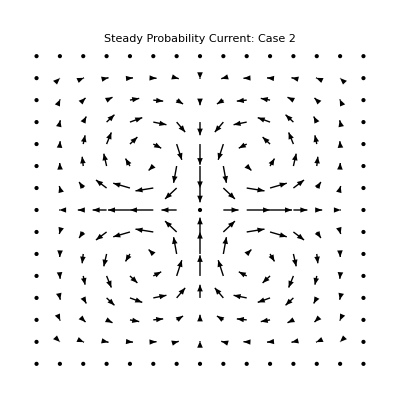

```mathematica
VectorFieldPlot[{J2X[x,y],J2Y[x,y]},{x,0,1},{y,0,1},PlotLabel->"Steady Probability Current: Case 2", LabelStyle->Directive[Bold, Red]]
```

```mathematica
V2X[x_,y_]:=J2X[x,y]/(P2[x,y]+0.000001)
V2Y[x_,y_]:=J2Y[x,y]/(P2[x,y]+0.000001)
```

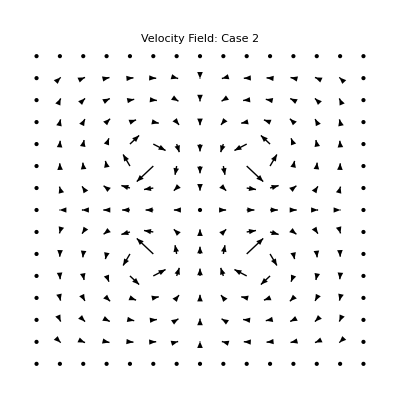

```mathematica
VectorFieldPlot[{V2X[x,y],V2Y[x,y]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field: Case 2", LabelStyle->Directive[Bold, Red]]
```

```mathematica
D[V2Y[x, y], x] - D[V2X[x, y], y]//Simplify//Chop
```

(0.000710612 Cos[3 π x] Cos[3 π y] Sin[π x] Sin[π y]-0.0000789568 Cos[π x] Cos[π y] Sin[3 π x] Sin[3 π y])/(1.×10^-6+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[3 π y]^2)^2

```mathematica
Ω2[x_,y_]:=(0.0007106115168784338 Cos[3 π x] Cos[3 π y] Sin[π x] Sin[π y]-0.00007895683520871486 Cos[π x] Cos[π y] Sin[3 π x] Sin[3 π y])/(1.*^-6+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[3 π y]^2)^2
```

```mathematica
Plot3D[Ω2[x,y],{x,.01,.99},{y,.01,.99}, PlotRange->{-10,10},PlotPoints->{100}, Ticks->False,PlotLabel->"Vorticity: Case 2", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

```mathematica
Ψ2
```

√2 ⅇ^(-10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]+ⅈ Sin[π x] Sin[3 π y])

```mathematica
Period2=1/(5π)
```

1/(5 π)

```mathematica
WaveFunction2[z_,y_,t_]:=√2 ⅇ^(-10 ⅈ π^2 t) (Sin[3 π x] Sin[π y]+ⅈ Sin[π x] Sin[3 π y])
```

```mathematica
Plot3D[Arg[ComplexExpand[WaveFunction2[x,y,0]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Initial Phase",Bold,Red]]

Plot3D[Arg[ComplexExpand[WaveFunction2[x,y,Period2/4]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time Period/4",Bold,Red]]

Plot3D[Arg[ComplexExpand[WaveFunction2[x,y,Period2/2]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time Period/2",Bold,Red]]
Plot3D[Arg[ComplexExpand[WaveFunction2[x,y,3 Period2/4]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 3Period/4",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### Application to Illustrative Case 3

This case gains interest from the fact that the probability density

-Graphics3D-

and associated current and vorticity are now time-dependent. I guess the position of an initial zero

```mathematica
P3[2/3,1/2,0]
```

0

(does the probability density vanish on a curve? hard to tell just by looking), which we know must move around cyclically.

Proceeding as before…

```mathematica
-ⅈ(Ψ1star D[Ψ3,x]-Ψ1 D[Ψ3star,x])//ComplexExpand//Simplify
-ⅈ(Ψ1star D[Ψ3,y]-Ψ1 D[Ψ3star,y])//ComplexExpand//Simplify
```

2/3 √2 π Sin[2 π x] Sin[π y]^2 (2+6 Cos[π (5 π t-y)]-6 Cos[π (5 π t-2 x-y)]+4 Cos[π (x-y)]-6 Cos[π (5 π t+2 x-y)]+2 Cos[2 π y]+6 Cos[π (5 π t+y)]-6 Cos[π (5 π t-2 x+y)]+4 Cos[π (x+y)]-6 Cos[π (5 π t+2 x+y)]-6 Sin[π (5 π t-3 x)]-6 Sin[π (5 π t+3 x)]+3 Sin[π (5 π t-y)]-3 Sin[π (5 π t-2 x-y)]-3 Sin[π (5 π t+2 x-y)]+3 Sin[π (5 π t+y)]-3 Sin[π (5 π t-2 x+y)]-3 Sin[π (5 π t+2 x+y)])

4/3 √2 π (-Cos[5 π^2 t] Cos[π y] Sin[3 π x] (2 Cos[10 π^2 t] Sin[π x] Sin[2 π y]+Sin[10 π^2 t] (2 Sin[2 π x] Sin[π y]+Sin[π x] Sin[2 π y]))+2 Cos[5 π^2 t]^2 (2 Cos[π x]+Cos[π y]) Sin[π x]^2 (-Sin[π y]+Sin[3 π y])+Sin[5 π^2 t] (4 Cos[2 π y] Sin[5 π^2 t] Sin[π x] Sin[2 π x] Sin[π y]+Cos[10 π^2 t] Cos[π y] Sin[3 π x] (2 Sin[2 π x] Sin[π y]+Sin[π x] Sin[2 π y])+Sin[π x] (-2 Cos[π y] Sin[10 π^2 t] Sin[3 π x] Sin[2 π y]+Sin[5 π^2 t] Sin[π x] Sin[4 π y])))

```mathematica
J3X[x_,y_,t_]:=2/3 √2 π Sin[2 π x] Sin[π y]^2 (2+6 Cos[π (5 π t-y)]-6 Cos[π (5 π t-2 x-y)]+4 Cos[π (x-y)]-6 Cos[π (5 π t+2 x-y)]+2 Cos[2 π y]+6 Cos[π (5 π t+y)]-6 Cos[π (5 π t-2 x+y)]+4 Cos[π (x+y)]-6 Cos[π (5 π t+2 x+y)]-6 Sin[π (5 π t-3 x)]-6 Sin[π (5 π t+3 x)]+3 Sin[π (5 π t-y)]-3 Sin[π (5 π t-2 x-y)]-3 Sin[π (5 π t+2 x-y)]+3 Sin[π (5 π t+y)]-3 Sin[π (5 π t-2 x+y)]-3 Sin[π (5 π t+2 x+y)])

J3Y[x_,y_,t_]:=4/3 √2 π (-Cos[5 π^2 t] Cos[π y] Sin[3 π x] (2 Cos[10 π^2 t] Sin[π x] Sin[2 π y]+Sin[10 π^2 t] (2 Sin[2 π x] Sin[π y]+Sin[π x] Sin[2 π y]))+2 Cos[5 π^2 t]^2 (2 Cos[π x]+Cos[π y]) Sin[π x]^2 (-Sin[π y]+Sin[3 π y])+Sin[5 π^2 t] (4 Cos[2 π y] Sin[5 π^2 t] Sin[π x] Sin[2 π x] Sin[π y]+Cos[10 π^2 t] Cos[π y] Sin[3 π x] (2 Sin[2 π x] Sin[π y]+Sin[π x] Sin[2 π y])+Sin[π x] (-2 Cos[π y] Sin[10 π^2 t] Sin[3 π x] Sin[2 π y]+Sin[5 π^2 t] Sin[π x] Sin[4 π y])))
```

Evidently the current configuration oscillates with

```mathematica
Period3=2/(5π)
```

2/(5 π)

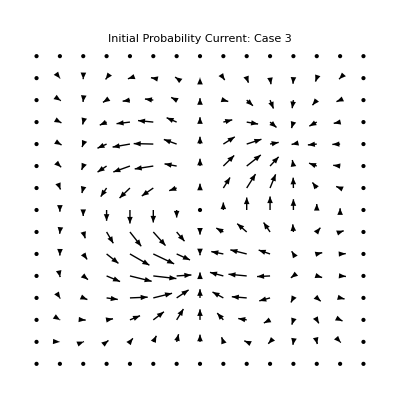

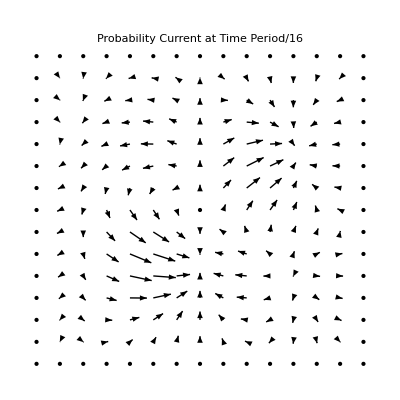

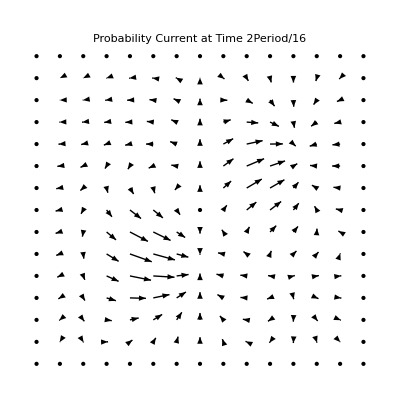

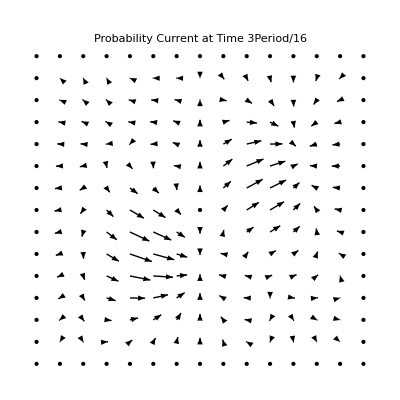

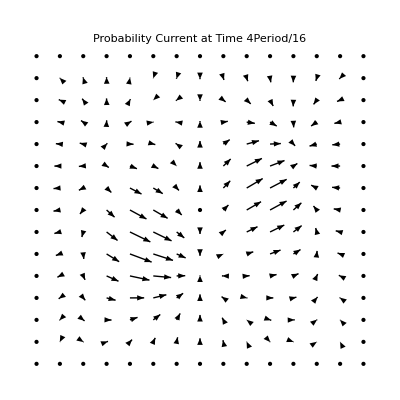

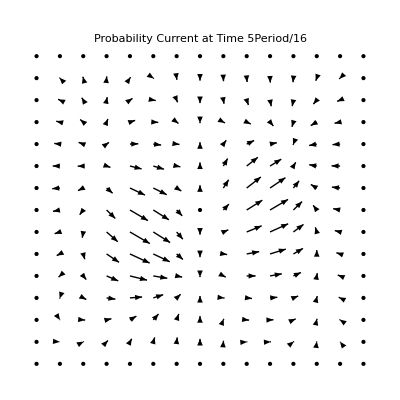

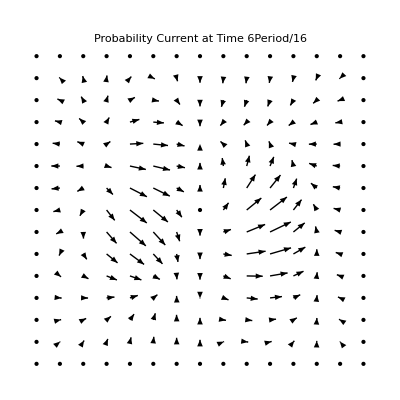

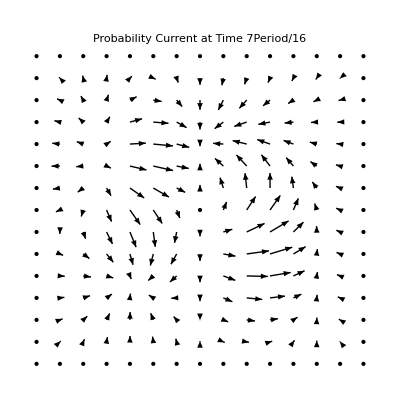

```mathematica
VectorFieldPlot[{J3X[x,y,0],J3Y[x,y,0]},{x,0,1},{y,0,1},PlotLabel->"Initial Probability Current: Case 3", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,Period3/16],J3Y[x,y,Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,2 Period3/16],J3Y[x,y,2 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 2Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,3 Period3/16],J3Y[x,y,3 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 3Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,4 Period3/16],J3Y[x,y,4 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 4Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,5 Period3/16],J3Y[x,y,5 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 5Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,6 Period3/16],J3Y[x,y,6 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 6Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,7 Period3/16],J3Y[x,y,7 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 7Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{J3X[x,y,8 Period3/16],J3Y[x,y,8 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Probability Current at Time 8Period/16", LabelStyle->Directive[Bold, Red]]
```

```mathematica
V3X[x_,y_,t_]:=J3X[x,y,t]/(P3[x,y,t]+0.000001)
V3Y[x_,y_,t_]:=J3Y[x,y,t]/(P3[x,y,t]+0.000001)
```

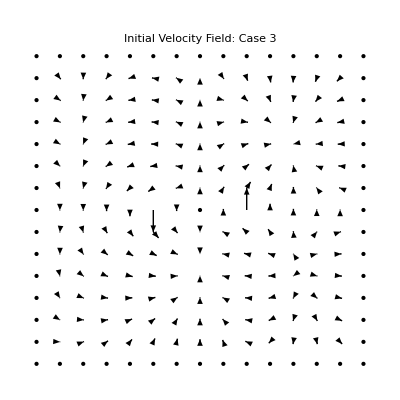

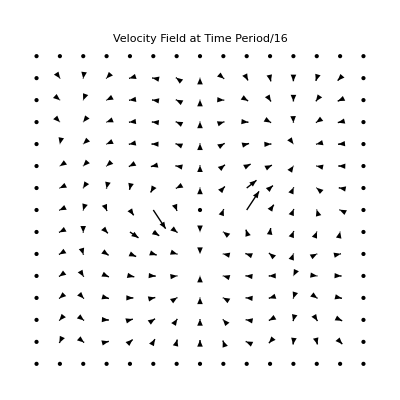

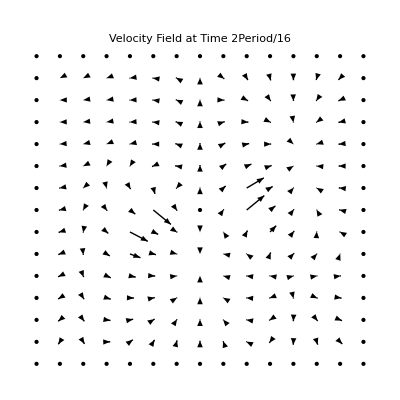

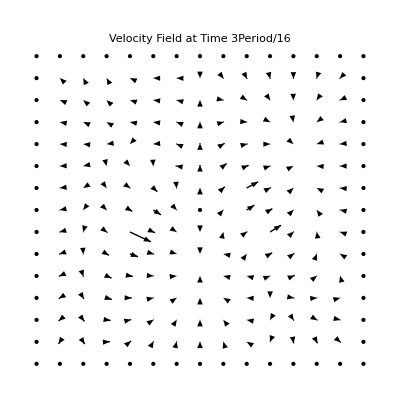

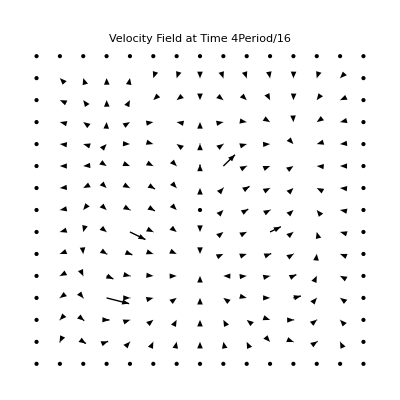

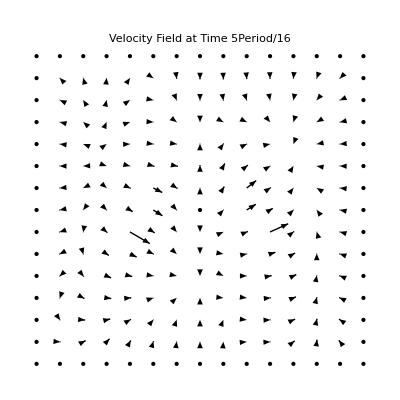

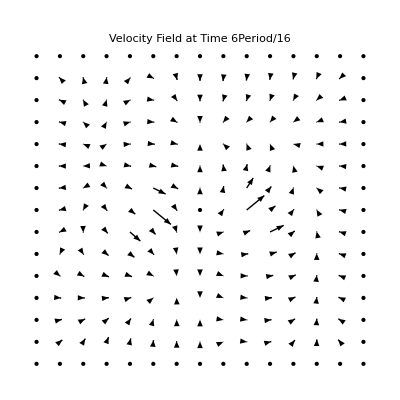

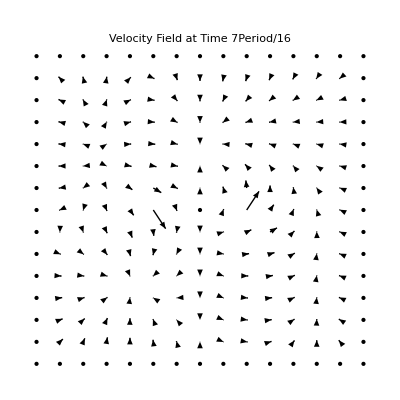

```mathematica
VectorFieldPlot[{V3X[x,y,0],V3Y[x,y,0]},{x,0,1},{y,0,1},PlotLabel->"Initial Velocity Field: Case 3", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,Period3/16],V3Y[x,y,Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,2 Period3/16],V3Y[x,y,2 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 2Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,3 Period3/16],V3Y[x,y,3 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 3Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,4 Period3/16],V3Y[x,y,4 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 4Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,5 Period3/16],V3Y[x,y,5 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 5Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,6 Period3/16],V3Y[x,y,6 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 6Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,7 Period3/16],V3Y[x,y,7 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 7Period/16", LabelStyle->Directive[Bold, Red]]

VectorFieldPlot[{V3X[x,y,8 Period3/16],V3Y[x,y,8 Period3/16]},{x,0,1},{y,0,1},PlotLabel->"Velocity Field at Time 8Period/16", LabelStyle->Directive[Bold, Red]]
```

We look finally to the motion of the complex phase:

```mathematica
Ψ3
```

√2 (ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ⅈ ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])

```mathematica
WaveFunction3[z_,y_,t_]:=√2 (ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ⅈ ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])
```

```mathematica
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,0]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Initial Phase",Bold,Red]]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,2 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 2Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,3 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 3Period/16",Bold,Red]]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,4 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 4Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,5 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 5Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,6 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 6Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,7 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 7Period/16",Bold,Red]]
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunction3[x,y,8 Period3/16]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase at time 8Period/16",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«6 more identical outputs»

Application to the case of a simple quantum Lissajous

We have demonstrated that the wavefunction

```mathematica
Φ=(1.1343346991218932 ⅇ^(-ⅈ t) Sin[π x]+0.8445618925620814 ⅇ^(-4 ⅈ t) Sin[2 π x]) (-1.144048972734524 ⅇ^(-9 ⅈ t) Sin[3 π y]-0.8313554883352129 ⅇ^(-16 ⅈ t) Sin[4 π y])
```

(1.13433 ⅇ^(-ⅈ t) Sin[π x]+0.844562 ⅇ^(-4 ⅈ t) Sin[2 π x]) (-1.14405 ⅇ^(-9 ⅈ t) Sin[3 π y]-0.831355 ⅇ^(-16 ⅈ t) Sin[4 π y])

```mathematica
Φstar=CompConj[Φ]
```

(1.13433 ⅇ^(ⅈ t) Sin[π x]+0.844562 ⅇ^(4 ⅈ t) Sin[2 π x]) (-1.14405 ⅇ^(9 ⅈ t) Sin[3 π y]-0.831355 ⅇ^(16 ⅈ t) Sin[4 π y])

leads to a probability density that moves with hardly more definition than a cloud

-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-

-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-

causes expected value of {x,y} to trace a nice crisp Lissajous figure of the form

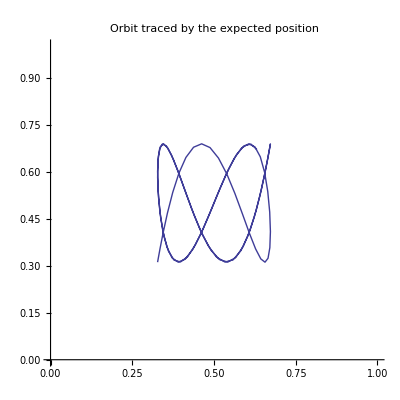

When we look to the probability current, we encounter expressions that are in general very complicated

```mathematica
-ⅈ(Φstar D[Φ,x]-Φ D[Φstar,x])//ComplexExpand//Chop
-ⅈ(Φstar D[Φ,y]-Φ D[Φstar,y])//ComplexExpand//Chop
```

15.7569 Cos[4 t] Cos[9 t]^2 Cos[2 π x] Sin[t] Sin[π x] Sin[3 π y]^2-15.7569 Cos[t] Cos[9 t]^2 Cos[2 π x] Sin[4 t] Sin[π x] Sin[3 π y]^2+15.7569 Cos[4 t] Cos[2 π x] Sin[t] Sin[9 t]^2 Sin[π x] Sin[3 π y]^2-15.7569 Cos[t] Cos[2 π x] Sin[4 t] Sin[9 t]^2 Sin[π x] Sin[3 π y]^2-7.87847 Cos[4 t] Cos[9 t]^2 Cos[π x] Sin[t] Sin[2 π x] Sin[3 π y]^2+7.87847 Cos[t] Cos[9 t]^2 Cos[π x] Sin[4 t] Sin[2 π x] Sin[3 π y]^2-7.87847 Cos[4 t] Cos[π x] Sin[t] Sin[9 t]^2 Sin[2 π x] Sin[3 π y]^2+7.87847 Cos[t] Cos[π x] Sin[4 t] Sin[9 t]^2 Sin[2 π x] Sin[3 π y]^2+22.9004 Cos[4 t] Cos[9 t] Cos[16 t] Cos[2 π x] Sin[t] Sin[π x] Sin[3 π y] Sin[4 π y]-22.9004 Cos[t] Cos[9 t] Cos[16 t] Cos[2 π x] Sin[4 t] Sin[π x] Sin[3 π y] Sin[4 π y]+22.9004 Cos[4 t] Cos[2 π x] Sin[t] Sin[9 t] Sin[16 t] Sin[π x] Sin[3 π y] Sin[4 π y]-22.9004 Cos[t] Cos[2 π x] Sin[4 t] Sin[9 t] Sin[16 t] Sin[π x] Sin[3 π y] Sin[4 π y]-11.4502 Cos[4 t] Cos[9 t] Cos[16 t] Cos[π x] Sin[t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+11.4502 Cos[t] Cos[9 t] Cos[16 t] Cos[π x] Sin[4 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]-11.4502 Cos[4 t] Cos[π x] Sin[t] Sin[9 t] Sin[16 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+11.4502 Cos[t] Cos[π x] Sin[4 t] Sin[9 t] Sin[16 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+8.32063 Cos[4 t] Cos[16 t]^2 Cos[2 π x] Sin[t] Sin[π x] Sin[4 π y]^2-8.32063 Cos[t] Cos[16 t]^2 Cos[2 π x] Sin[4 t] Sin[π x] Sin[4 π y]^2+8.32063 Cos[4 t] Cos[2 π x] Sin[t] Sin[16 t]^2 Sin[π x] Sin[4 π y]^2-8.32063 Cos[t] Cos[2 π x] Sin[4 t] Sin[16 t]^2 Sin[π x] Sin[4 π y]^2-4.16031 Cos[4 t] Cos[16 t]^2 Cos[π x] Sin[t] Sin[2 π x] Sin[4 π y]^2+4.16031 Cos[t] Cos[16 t]^2 Cos[π x] Sin[4 t] Sin[2 π x] Sin[4 π y]^2-4.16031 Cos[4 t] Cos[π x] Sin[t] Sin[16 t]^2 Sin[2 π x] Sin[4 π y]^2+4.16031 Cos[t] Cos[π x] Sin[4 t] Sin[16 t]^2 Sin[2 π x] Sin[4 π y]^2

30.7577 Cos[t]^2 Cos[16 t] Cos[4 π y] Sin[9 t] Sin[π x]^2 Sin[3 π y]+30.7577 Cos[16 t] Cos[4 π y] Sin[t]^2 Sin[9 t] Sin[π x]^2 Sin[3 π y]-30.7577 Cos[t]^2 Cos[9 t] Cos[4 π y] Sin[16 t] Sin[π x]^2 Sin[3 π y]-30.7577 Cos[9 t] Cos[4 π y] Sin[t]^2 Sin[16 t] Sin[π x]^2 Sin[3 π y]+45.8009 Cos[t] Cos[4 t] Cos[16 t] Cos[4 π y] Sin[9 t] Sin[π x] Sin[2 π x] Sin[3 π y]+45.8009 Cos[16 t] Cos[4 π y] Sin[t] Sin[4 t] Sin[9 t] Sin[π x] Sin[2 π x] Sin[3 π y]-45.8009 Cos[t] Cos[4 t] Cos[9 t] Cos[4 π y] Sin[16 t] Sin[π x] Sin[2 π x] Sin[3 π y]-45.8009 Cos[9 t] Cos[4 π y] Sin[t] Sin[4 t] Sin[16 t] Sin[π x] Sin[2 π x] Sin[3 π y]+17.0504 Cos[4 t]^2 Cos[16 t] Cos[4 π y] Sin[9 t] Sin[2 π x]^2 Sin[3 π y]+17.0504 Cos[16 t] Cos[4 π y] Sin[4 t]^2 Sin[9 t] Sin[2 π x]^2 Sin[3 π y]-17.0504 Cos[4 t]^2 Cos[9 t] Cos[4 π y] Sin[16 t] Sin[2 π x]^2 Sin[3 π y]-17.0504 Cos[9 t] Cos[4 π y] Sin[4 t]^2 Sin[16 t] Sin[2 π x]^2 Sin[3 π y]-23.0683 Cos[t]^2 Cos[16 t] Cos[3 π y] Sin[9 t] Sin[π x]^2 Sin[4 π y]-23.0683 Cos[16 t] Cos[3 π y] Sin[t]^2 Sin[9 t] Sin[π x]^2 Sin[4 π y]+23.0683 Cos[t]^2 Cos[9 t] Cos[3 π y] Sin[16 t] Sin[π x]^2 Sin[4 π y]+23.0683 Cos[9 t] Cos[3 π y] Sin[t]^2 Sin[16 t] Sin[π x]^2 Sin[4 π y]-34.3507 Cos[t] Cos[4 t] Cos[16 t] Cos[3 π y] Sin[9 t] Sin[π x] Sin[2 π x] Sin[4 π y]-34.3507 Cos[16 t] Cos[3 π y] Sin[t] Sin[4 t] Sin[9 t] Sin[π x] Sin[2 π x] Sin[4 π y]+34.3507 Cos[t] Cos[4 t] Cos[9 t] Cos[3 π y] Sin[16 t] Sin[π x] Sin[2 π x] Sin[4 π y]+34.3507 Cos[9 t] Cos[3 π y] Sin[t] Sin[4 t] Sin[16 t] Sin[π x] Sin[2 π x] Sin[4 π y]-12.7878 Cos[4 t]^2 Cos[16 t] Cos[3 π y] Sin[9 t] Sin[2 π x]^2 Sin[4 π y]-12.7878 Cos[16 t] Cos[3 π y] Sin[4 t]^2 Sin[9 t] Sin[2 π x]^2 Sin[4 π y]+12.7878 Cos[4 t]^2 Cos[9 t] Cos[3 π y] Sin[16 t] Sin[2 π x]^2 Sin[4 π y]+12.7878 Cos[9 t] Cos[3 π y] Sin[4 t]^2 Sin[16 t] Sin[2 π x]^2 Sin[4 π y]

```mathematica
JLissX[x_,y_,t_]:=15.756936833748924 Cos[4 t] Cos[9 t]^2 Cos[2 π x] Sin[t] Sin[π x] Sin[3 π y]^2-15.756936833748924 Cos[t] Cos[9 t]^2 Cos[2 π x] Sin[4 t] Sin[π x] Sin[3 π y]^2+15.756936833748924 Cos[4 t] Cos[2 π x] Sin[t] Sin[9 t]^2 Sin[π x] Sin[3 π y]^2-15.756936833748924 Cos[t] Cos[2 π x] Sin[4 t] Sin[9 t]^2 Sin[π x] Sin[3 π y]^2-7.878468416874462 Cos[4 t] Cos[9 t]^2 Cos[π x] Sin[t] Sin[2 π x] Sin[3 π y]^2+7.878468416874462 Cos[t] Cos[9 t]^2 Cos[π x] Sin[4 t] Sin[2 π x] Sin[3 π y]^2-7.878468416874462 Cos[4 t] Cos[π x] Sin[t] Sin[9 t]^2 Sin[2 π x] Sin[3 π y]^2+7.878468416874462 Cos[t] Cos[π x] Sin[4 t] Sin[9 t]^2 Sin[2 π x] Sin[3 π y]^2+22.900446096774214 Cos[4 t] Cos[9 t] Cos[16 t] Cos[2 π x] Sin[t] Sin[π x] Sin[3 π y] Sin[4 π y]-22.900446096774214 Cos[t] Cos[9 t] Cos[16 t] Cos[2 π x] Sin[4 t] Sin[π x] Sin[3 π y] Sin[4 π y]+22.900446096774214 Cos[4 t] Cos[2 π x] Sin[t] Sin[9 t] Sin[16 t] Sin[π x] Sin[3 π y] Sin[4 π y]-22.900446096774214 Cos[t] Cos[2 π x] Sin[4 t] Sin[9 t] Sin[16 t] Sin[π x] Sin[3 π y] Sin[4 π y]-11.450223048387107 Cos[4 t] Cos[9 t] Cos[16 t] Cos[π x] Sin[t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+11.450223048387107 Cos[t] Cos[9 t] Cos[16 t] Cos[π x] Sin[4 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]-11.450223048387107 Cos[4 t] Cos[π x] Sin[t] Sin[9 t] Sin[16 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+11.450223048387107 Cos[t] Cos[π x] Sin[4 t] Sin[9 t] Sin[16 t] Sin[2 π x] Sin[3 π y] Sin[4 π y]+8.320627875908158 Cos[4 t] Cos[16 t]^2 Cos[2 π x] Sin[t] Sin[π x] Sin[4 π y]^2-8.320627875908158 Cos[t] Cos[16 t]^2 Cos[2 π x] Sin[4 t] Sin[π x] Sin[4 π y]^2+8.320627875908158 Cos[4 t] Cos[2 π x] Sin[t] Sin[16 t]^2 Sin[π x] Sin[4 π y]^2-8.320627875908158 Cos[t] Cos[2 π x] Sin[4 t] Sin[16 t]^2 Sin[π x] Sin[4 π y]^2-4.160313937954079 Cos[4 t] Cos[16 t]^2 Cos[π x] Sin[t] Sin[2 π x] Sin[4 π y]^2+4.160313937954079 Cos[t] Cos[16 t]^2 Cos[π x] Sin[4 t] Sin[2 π x] Sin[4 π y]^2-4.160313937954079 Cos[4 t] Cos[π x] Sin[t] Sin[16 t]^2 Sin[2 π x] Sin[4 π y]^2+4.160313937954079 Cos[t] Cos[π x] Sin[4 t] Sin[16 t]^2 Sin[2 π x] Sin[4 π y]^2
```

```mathematica
JLissY[x_,y_,t_]:=30.7576873426503 Cos[t]^2 Cos[16 t] Cos[4 π y] Sin[9 t] Sin[π x]^2 Sin[3 π y]+30.7576873426503 Cos[16 t] Cos[4 π y] Sin[t]^2 Sin[9 t] Sin[π x]^2 Sin[3 π y]-30.7576873426503 Cos[t]^2 Cos[9 t] Cos[4 π y] Sin[16 t] Sin[π x]^2 Sin[3 π y]-30.7576873426503 Cos[9 t] Cos[4 π y] Sin[t]^2 Sin[16 t] Sin[π x]^2 Sin[3 π y]+45.80089219354843 Cos[t] Cos[4 t] Cos[16 t] Cos[4 π y] Sin[9 t] Sin[π x] Sin[2 π x] Sin[3 π y]+45.80089219354843 Cos[16 t] Cos[4 π y] Sin[t] Sin[4 t] Sin[9 t] Sin[π x] Sin[2 π x] Sin[3 π y]-45.80089219354843 Cos[t] Cos[4 t] Cos[9 t] Cos[4 π y] Sin[16 t] Sin[π x] Sin[2 π x] Sin[3 π y]-45.80089219354843 Cos[9 t] Cos[4 π y] Sin[t] Sin[4 t] Sin[16 t] Sin[π x] Sin[2 π x] Sin[3 π y]+17.050385667457427 Cos[4 t]^2 Cos[16 t] Cos[4 π y] Sin[9 t] Sin[2 π x]^2 Sin[3 π y]+17.050385667457427 Cos[16 t] Cos[4 π y] Sin[4 t]^2 Sin[9 t] Sin[2 π x]^2 Sin[3 π y]-17.050385667457427 Cos[4 t]^2 Cos[9 t] Cos[4 π y] Sin[16 t] Sin[2 π x]^2 Sin[3 π y]-17.050385667457427 Cos[9 t] Cos[4 π y] Sin[4 t]^2 Sin[16 t] Sin[2 π x]^2 Sin[3 π y]-23.06826550698773 Cos[t]^2 Cos[16 t] Cos[3 π y] Sin[9 t] Sin[π x]^2 Sin[4 π y]-23.06826550698773 Cos[16 t] Cos[3 π y] Sin[t]^2 Sin[9 t] Sin[π x]^2 Sin[4 π y]+23.06826550698773 Cos[t]^2 Cos[9 t] Cos[3 π y] Sin[16 t] Sin[π x]^2 Sin[4 π y]+23.06826550698773 Cos[9 t] Cos[3 π y] Sin[t]^2 Sin[16 t] Sin[π x]^2 Sin[4 π y]-34.35066914516132 Cos[t] Cos[4 t] Cos[16 t] Cos[3 π y] Sin[9 t] Sin[π x] Sin[2 π x] Sin[4 π y]-34.35066914516132 Cos[16 t] Cos[3 π y] Sin[t] Sin[4 t] Sin[9 t] Sin[π x] Sin[2 π x] Sin[4 π y]+34.35066914516132 Cos[t] Cos[4 t] Cos[9 t] Cos[3 π y] Sin[16 t] Sin[π x] Sin[2 π x] Sin[4 π y]+34.35066914516132 Cos[9 t] Cos[3 π y] Sin[t] Sin[4 t] Sin[16 t] Sin[π x] Sin[2 π x] Sin[4 π y]-12.78778925059307 Cos[4 t]^2 Cos[16 t] Cos[3 π y] Sin[9 t] Sin[2 π x]^2 Sin[4 π y]-12.78778925059307 Cos[16 t] Cos[3 π y] Sin[4 t]^2 Sin[9 t] Sin[2 π x]^2 Sin[4 π y]+12.78778925059307 Cos[4 t]^2 Cos[9 t] Cos[3 π y] Sin[16 t] Sin[2 π x]^2 Sin[4 π y]+12.78778925059307 Cos[9 t] Cos[3 π y] Sin[4 t]^2 Sin[16 t] Sin[2 π x]^2 Sin[4 π y]
```

—though at certain times they do assume greatly simpified form

```mathematica
JLissX[x,y,0]
JLissY[x,y,0]
```

0

0

```mathematica
JLissX[x,y,π]
JLissY[x,y,π]
```

0

0

```mathematica
JLissX[x,y,1]
JLissY[x,y,1]
```

-2.22362 Cos[2 π x] Sin[π x] Sin[3 π y]^2+1.11181 Cos[π x] Sin[2 π x] Sin[3 π y]^2-2.43639 Cos[2 π x] Sin[π x] Sin[3 π y] Sin[4 π y]+1.2182 Cos[π x] Sin[2 π x] Sin[3 π y] Sin[4 π y]-1.17421 Cos[2 π x] Sin[π x] Sin[4 π y]^2+0.587104 Cos[π x] Sin[2 π x] Sin[4 π y]^2

-20.2074 Cos[4 π y] Sin[π x]^2 Sin[3 π y]+29.7894 Cos[4 π y] Sin[π x] Sin[2 π x] Sin[3 π y]-11.2019 Cos[4 π y] Sin[2 π x]^2 Sin[3 π y]+15.1555 Cos[3 π y] Sin[π x]^2 Sin[4 π y]-22.3421 Cos[3 π y] Sin[π x] Sin[2 π x] Sin[4 π y]+8.40141 Cos[3 π y] Sin[2 π x]^2 Sin[4 π y]

—and which give rise to not-very-informative vector field plots:

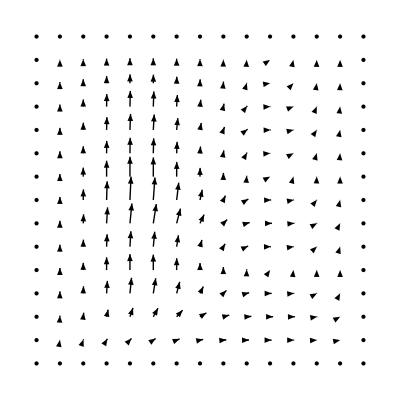
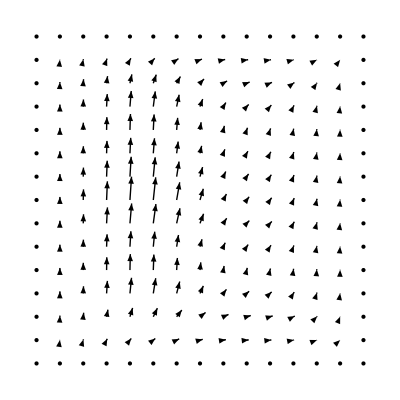
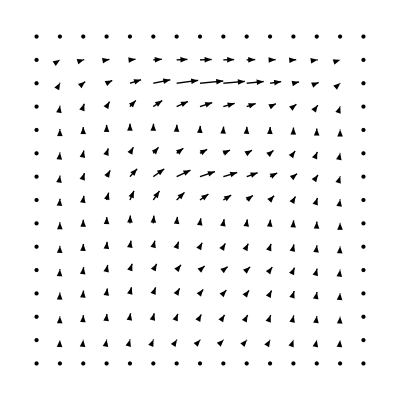
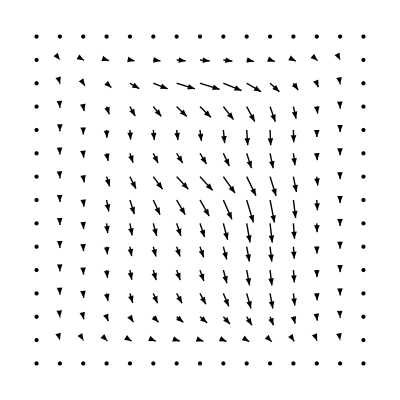
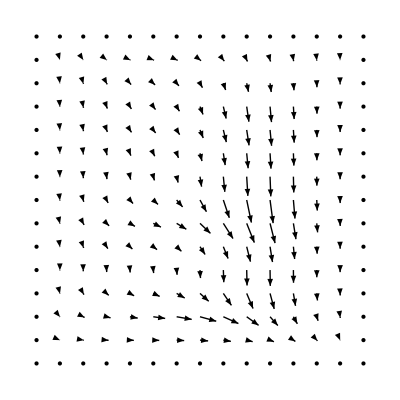
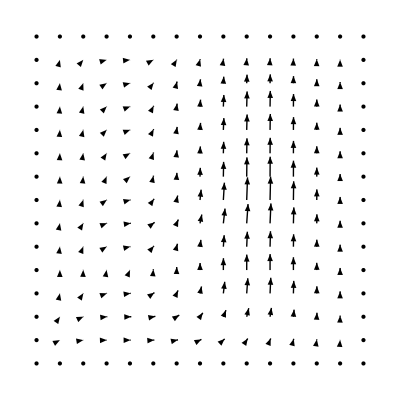
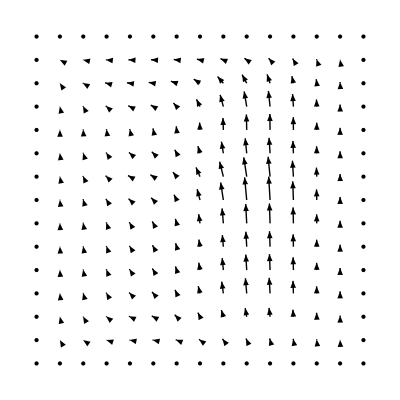
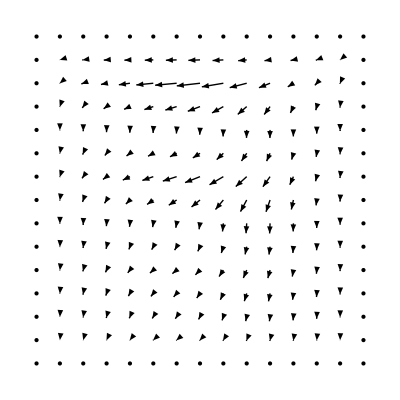
(0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14 | -Graphics-
15 | -Graphics-
16 | -Graphics-
17 | -Graphics-
18 | -Graphics-
19 | -Graphics-
20 | -Graphics-
21 | -Graphics-
22 | -Graphics-
23 | -Graphics-
24 | -Graphics-
25 | -Graphics-)

```mathematica
Table[{k,VectorFieldPlot[Evaluate[{JLissX[x,y,k/5+.0001],JLissY[x,y,k/5+.0001]}],{x,0,1},{y,0,1}]},{k,0,25}]//MatrixForm
```

When we look finally to the phase of the wavefunction,

```mathematica
Φ
```

(1.13433 ⅇ^(-ⅈ t) Sin[π x]+0.844562 ⅇ^(-4 ⅈ t) Sin[2 π x]) (-1.14405 ⅇ^(-9 ⅈ t) Sin[3 π y]-0.831355 ⅇ^(-16 ⅈ t) Sin[4 π y])

```mathematica
ComplexExpand[Φ]
```

-1.29773 Cos[t] Cos[9 t] Sin[π x] Sin[3 π y]+1.29773 Sin[t] Sin[9 t] Sin[π x] Sin[3 π y]-0.96622 Cos[4 t] Cos[9 t] Sin[2 π x] Sin[3 π y]+0.96622 Sin[4 t] Sin[9 t] Sin[2 π x] Sin[3 π y]-0.943035 Cos[t] Cos[16 t] Sin[π x] Sin[4 π y]+0.943035 Sin[t] Sin[16 t] Sin[π x] Sin[4 π y]-0.702131 Cos[4 t] Cos[16 t] Sin[2 π x] Sin[4 π y]+0.702131 Sin[4 t] Sin[16 t] Sin[2 π x] Sin[4 π y]+ⅈ (1.29773 Cos[9 t] Sin[t] Sin[π x] Sin[3 π y]+1.29773 Cos[t] Sin[9 t] Sin[π x] Sin[3 π y]+0.96622 Cos[9 t] Sin[4 t] Sin[2 π x] Sin[3 π y]+0.96622 Cos[4 t] Sin[9 t] Sin[2 π x] Sin[3 π y]+0.943035 Cos[16 t] Sin[t] Sin[π x] Sin[4 π y]+0.943035 Cos[t] Sin[16 t] Sin[π x] Sin[4 π y]+0.702131 Cos[16 t] Sin[4 t] Sin[2 π x] Sin[4 π y]+0.702131 Cos[4 t] Sin[16 t] Sin[2 π x] Sin[4 π y])

```mathematica
WaveFunctionΦ[x_,y_,t_]:=(1.1343346991218932 ⅇ^(-ⅈ t) Sin[π x]+0.8445618925620814 ⅇ^(-4 ⅈ t) Sin[2 π x]) (-1.144048972734524 ⅇ^(-9 ⅈ t) Sin[3 π y]-0.8313554883352129 ⅇ^(-16 ⅈ t) Sin[4 π y])
```

we are led to figures

```mathematica
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,1/5 k]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},  Ticks->{{},{},{-π,π}}]
```

```mathematica
Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,0/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,1/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,2/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,3/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,4/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]

Plot3D[Evaluate[Arg[ComplexExpand[WaveFunctionΦ[x,y,5/5]]]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->20 , Ticks->{{},{},{-π,π}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

that are complicated at every instant, and that move in complicated ways.

### Appliction to Chen's quantum Lissajous state

We had

```mathematica
Ψ[x_,y_,m_,n_]:=2 Sin[m π x]Sin[n π y]
Chen[x_,y_,n_, p_, q_,ϕ_]:=1/2^(n/2)∑_(k=0)^n √Binomial[n,k] ⅇ^(ⅈ k ϕ)Ψ[p x,q y,k+1,n-k+1]
```

which led to real-valued intial state like this

```mathematica
Chen[x,y,10, 7,3,0]
```

1/32 (2 Sin[77 π x] Sin[3 π y]+2 √10 Sin[70 π x] Sin[6 π y]+6 √5 Sin[63 π x] Sin[9 π y]+4 √30 Sin[56 π x] Sin[12 π y]+2 √210 Sin[49 π x] Sin[15 π y]+12 √7 Sin[42 π x] Sin[18 π y]+2 √210 Sin[35 π x] Sin[21 π y]+4 √30 Sin[28 π x] Sin[24 π y]+6 √5 Sin[21 π x] Sin[27 π y]+2 √10 Sin[14 π x] Sin[30 π y]+2 Sin[7 π x] Sin[33 π y])

```mathematica
ChenΨ[x_,y_]:=1/32 (2 Sin[77 π x] Sin[3 π y]+2 √10 Sin[70 π x] Sin[6 π y]+6 √5 Sin[63 π x] Sin[9 π y]+4 √30 Sin[56 π x] Sin[12 π y]+2 √210 Sin[49 π x] Sin[15 π y]+12 √7 Sin[42 π x] Sin[18 π y]+2 √210 Sin[35 π x] Sin[21 π y]+4 √30 Sin[28 π x] Sin[24 π y]+6 √5 Sin[21 π x] Sin[27 π y]+2 √10 Sin[14 π x] Sin[30 π y]+2 Sin[7 π x] Sin[33 π y])
```

and which led to probability density plots like this:

-Graphics-

When we look to the definition of probability current

JX=-ⅈ(Ψstar D[Ψ,x]-Ψ D[Ψstar,x])//ComplexExpand
JY=-ⅈ(Ψstar D[Ψ,y]-Ψ D[Ψstar,y])//ComplexExpand

we see that to avoid the uninteresting statements

JX =0
JY =0

the state Ψ must be complex. The Chen state to which we look previously was, however, real, so we look now to the Chen state

```mathematica
Chen[x,y,10, 7,3,π/3]//ComplexExpand
```

-1/32 Sin[77 π x] Sin[3 π y]-1/8 √(5/2) Sin[70 π x] Sin[6 π y]-3/32 √5 Sin[63 π x] Sin[9 π y]+1/8 √(15/2) Sin[56 π x] Sin[12 π y]+1/8 √(105/2) Sin[49 π x] Sin[15 π y]+3/16 √7 Sin[42 π x] Sin[18 π y]-1/16 √(105/2) Sin[35 π x] Sin[21 π y]-1/4 √(15/2) Sin[28 π x] Sin[24 π y]-3/32 √5 Sin[21 π x] Sin[27 π y]+1/16 √(5/2) Sin[14 π x] Sin[30 π y]+ⅈ (-1/32 √3 Sin[77 π x] Sin[3 π y]+3/32 √15 Sin[63 π x] Sin[9 π y]+3/8 √(5/2) Sin[56 π x] Sin[12 π y]-3/16 √21 Sin[42 π x] Sin[18 π y]-3/16 √(35/2) Sin[35 π x] Sin[21 π y]+3/32 √15 Sin[21 π x] Sin[27 π y]+1/16 √(15/2) Sin[14 π x] Sin[30 π y])+1/16 Sin[7 π x] Sin[33 π y]

```mathematica
ChenΨ=-1/32 Sin[77 π x] Sin[3 π y]-1/8 √(5/2) Sin[70 π x] Sin[6 π y]-3/32 √5 Sin[63 π x] Sin[9 π y]+1/8 √(15/2) Sin[56 π x] Sin[12 π y]+1/8 √(105/2) Sin[49 π x] Sin[15 π y]+3/16 √7 Sin[42 π x] Sin[18 π y]-1/16 √(105/2) Sin[35 π x] Sin[21 π y]-1/4 √(15/2) Sin[28 π x] Sin[24 π y]-3/32 √5 Sin[21 π x] Sin[27 π y]+1/16 √(5/2) Sin[14 π x] Sin[30 π y]+ⅈ (-1/32 √3 Sin[77 π x] Sin[3 π y]+3/32 √15 Sin[63 π x] Sin[9 π y]+3/8 √(5/2) Sin[56 π x] Sin[12 π y]-3/16 √21 Sin[42 π x] Sin[18 π y]-3/16 √(35/2) Sin[35 π x] Sin[21 π y]+3/32 √15 Sin[21 π x] Sin[27 π y]+1/16 √(15/2) Sin[14 π x] Sin[30 π y])+1/16 Sin[7 π x] Sin[33 π y];
```

```mathematica
RealChenΨ=-1/32 Sin[77 π x] Sin[3 π y]-1/8 √(5/2) Sin[70 π x] Sin[6 π y]-3/32 √5 Sin[63 π x] Sin[9 π y]+1/8 √(15/2) Sin[56 π x] Sin[12 π y]+1/8 √(105/2) Sin[49 π x] Sin[15 π y]+3/16 √7 Sin[42 π x] Sin[18 π y]-1/16 √(105/2) Sin[35 π x] Sin[21 π y]-1/4 √(15/2) Sin[28 π x] Sin[24 π y]-3/32 √5 Sin[21 π x] Sin[27 π y]+1/16 √(5/2) Sin[14 π x] Sin[30 π y]+1/16 Sin[7 π x] Sin[33 π y];
ImagChenΨ=-1/32 √3 Sin[77 π x] Sin[3 π y]+3/32 √15 Sin[63 π x] Sin[9 π y]+3/8 √(5/2) Sin[56 π x] Sin[12 π y]-3/16 √21 Sin[42 π x] Sin[18 π y]-3/16 √(35/2) Sin[35 π x] Sin[21 π y]+3/32 √15 Sin[21 π x] Sin[27 π y]+1/16 √(15/2) Sin[14 π x] Sin[30 π y];
```

```mathematica
DensityPlot[Evaluate[RealChenΨ^2+ImagChenΨ^2],{x,0,1},{y,0,1}, PlotPoints->100]
```

-Graphics-

```mathematica
DensityPlot[Evaluate[RealChenΨ^2+ImagChenΨ^2],{x,0,4/7},{y,0,2/3}, PlotPoints->100]
```

-Graphics-

```mathematica
ChenΨstar=RealChenΨ-ⅈ ImagChenΨ;
```

```mathematica
JXChen=-ⅈ(ChenΨstar D[ChenΨ,x]-ChenΨ D[ChenΨstar,x])//ComplexExpand;
JYChen=-ⅈ(ChenΨstar D[ChenΨ,y]-ChenΨ D[ChenΨstar,y])//ComplexExpand;
```

```mathematica
Length[JXChen]
Length[JYChen]
```

80

80

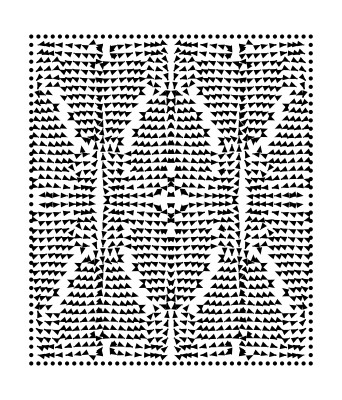

```mathematica
VectorFieldPlot[{JXChen,JYChen},{x,0,4/7},{y,0,2/3}, PlotPoints->40]
```

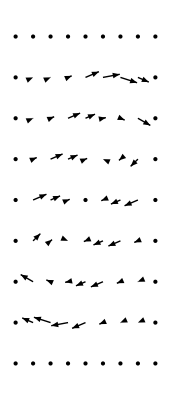

```mathematica
VectorFieldPlot[{JXChen,JYChen},{x,0,1/7},{y,0,1/3}, PlotPoints->9]
```

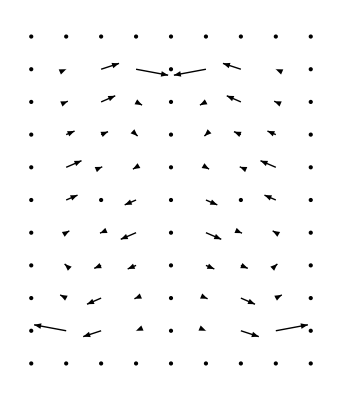

```mathematica
VectorFieldPlot[{JXChen,JYChen},{x,0,2/7,1/28},{y,0,1/3, 1/30}]
```